```mathematica
R=100; (* X=R^2 *)
t=Flatten[Table[{i,j},{i,-R,R},{j,0,R}],1];
t=Select[t, Norm[#]≤ R & ];
angles=Table[VectorAngle[t[[i]],{1,0}],{i,1,Length[t]}];
```

```mathematica
d=Table[{j,Divide[Variance
[Last[HistogramList[angles,{1,π/2+1,(π/2)/Round[R^(2*j)]}]]],3/π R^(2*(1-j))*Log[R]]},{j,0.25,1.4,0.05}];
f=ListPlot[d];
```

```mathematica
zeta2'=π^2/6*(EulerGamma+Log[2]-12*Log[1.282427129]+Log[π]);
Dphi'=-4*π/4*6/π^2+2*(0.1929)*6/π^2-2*2*π/4*zeta2'*36/π^4;
Gz=3*4.1; (* Hard coded for now, use computation in the future *)
Delta1=2 π^2*((9*EulerGamma)/π+Dphi')-Gz;LowerOrd3=Delta1/(12*π*Log[R])
```

0.0504478

```mathematica
IntegralWithLog = 1-EulerGamma-Log[2π];
kappa=2*6*π*Log[π/2]+3π*(-8)+Gz-π^2*2*((9*EulerGamma)/π+Dphi');
Delta2=2*6*π*IntegralWithLog-kappa;
LowerOrd2=Delta2/(12*π*Log[R])
```

0.0793989

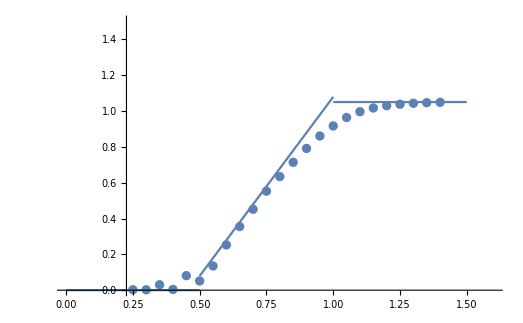

```mathematica
g1=Plot[0,{x,0,0.5}];
g2=Plot[2x-1+LowerOrd2,{x,0.5,1}];
g3=Plot[1+LowerOrd3,{x,1,1.5}];
Show[f,g1,g2,g3,PlotRange->{{0,1.6},{0,1.5}}]
```